# Simplifying identity

We first check the N=2 case explicitly and then we define functions for general N to check the general N case.

## N=2 case

We attempt to generalize Lemma 6.3 from Liu-Saenz-Wang for the XXZ

```mathematica
M1 =({{(x1 + z2 -2 d x1 z2)/(1- x1 z1), (x1 +z1 - 2 d x1 z1)/(1- x1 z2)}, {(x2 + z2 - 2d x2 z2)/(1- x2 z1), (x2 + z1 - 2 d x2 z1)/(1- x2 z2)}});
L = Det[M1];
```

```mathematica
Simplify[L]
```

((x1-x2) (z1-z2) (1-2 d x1 z1 z2+z1 (z2-2 d x2 z2)+x1 x2 (1+z1 z2+4 d^2 z1 z2-2 d (z1+z2))))/((-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2))

```mathematica
g[x1_, x2_, z1_, z2_]:= ((x1-x2) (z1-z2) (1-2 d x1 z1 z2+z1 (z2-2 d x2 z2)+x1 x2 (1+z1 z2+4 d^2 z1 z2-2 d (z1+z2))))/((-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2));
```

```mathematica
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 2}]]
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 1}]]
Simplify[1/((x2-x1)(z2-z1))SeriesCoefficient[Numerator[Together[L]], {d, 0, 0}]]
```

4 x1 x2 z1 z2

-2 (x1 z1 z2+x2 z1 z2+x1 x2 (z1+z2))

(1+x1 x2) (1+z1 z2)

```mathematica
term3 =((1 + x1 x2 - 2 d x1)(1 + z1 z2 - 2 d z1)x2 z2)/((1- x1 z1)(1- x2 z2))-((1 + x1 x2 - 2 d x2)(1 + z1 z2 - 2d z1)x1 z2)/((1- x2 z1)(1- x1 z2))-((1 + x1 x2 - 2 d x1)(1 + z1 z2 - 2 d z2)x2 z1)/((1- x1 z2)(1- x2 z1))+((1 + x1 x2 - 2 d x2)(1 + z1 z2 - 2 d z2)x1 z1)/((1- x1 z1)(1- x2 z2))-L;
```

```mathematica
Denominator[Simplify[Together[term3]]]
```

(-1+x1 z1) (-1+x2 z1) (-1+x1 z2) (-1+x2 z2)

```mathematica
Numerator[Simplify[Together[term3]]]
```

x1 (x1-x2) x2 z1 (z1-z2) z2 (4 d^2-2 d (x1+x2+z1+z2)+(1+x1 x2) (1+z1 z2))

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[term3]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2 x1-2 x2-2 z1-2 z2

1+x1 x2+z1 z2+x1 x2 z1 z2

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[L]]]/(x1 x2 z1 z2(x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2/x1-2/x2-2/z1-2/z2

1+1/(x1 x2)+1/(z1 z2)+1/(x1 x2 z1 z2)

```mathematica
SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 2}]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 1}]]
Expand[SeriesCoefficient[Simplify[Numerator[Simplify[Together[g[1/x1, 1/x2, 1/z1, 1/z2]]]]/((x2-x1)(z2-z1))], {d, 0, 0}]]
```

4

-2 x1-2 x2-2 z1-2 z2

1+x1 x2+z1 z2+x1 x2 z1 z2

```mathematica
Simplify[term3/g[1/x1, 1/x2, 1/z1, 1/z2]]
```

x1 x2 z1 z2

## Automatic Check

## Functions

### G-function

- d is a real number
- x is the variable name
- Is is a set of (disjoint) subsets (of {1, ..., N})

```mathematica
G[d_, x_, Is_, s_]:=Module[{i, j,k},
k = Length[Is];
Return[Product[Product[(1 + x[Is[[s[[i]]]][[a]]]x[Is[[s[[j]]]][[b]]] - 2d x[Is[[s[[i]]]][[a]]])If[Is[[s[[i]]]][[a]]>Is[[s[[j]]]][[b]], -1, 1] ,{a, 1, Length[Is[[s[[i]]]]]}, {b, 1, Length[Is[[s[[j]]]]]}], {i, 1, k-1}, {j, i+1, k}]];
]
```

```mathematica
G[d, x, {{1}, {2}}, {1,2}]
G[d, x, {{1}, {2}}, {2,1}]
```

1-2 d x[1]+x[1] x[2]

-1+2 d x[2]-x[1] x[2]

### F-function

```mathematica
F[x_,z_, I1_, I2_ ]:= Product[x[I1[[k]]], {k, 1, Length[I1]}]Product[z[I2[[k]]], {k, 1, Length[I2]}];
```

### Λ-function

```mathematica
Λ[d_, x_, z_, I1_, I2_]:=Module[{i, j, k, l,M}, 
k = Length[I1];
(*If the subsets are not the same length, return 0.*)
If[k!= Length[I2], Return[0]];
If[k==0, 1];
Return[ Det[Table[Product[If[l!= j, x[I1[[i]]] +z[I2[[l]]]- 2 d x[I1[[i]]] z[I2[[l]]], 1], {l, 1, k}]/(1- x[I1[[i]]]z[I2[[j]]]) , {i, 1, k}, {j, 1, k}]]];
]
```

## Left side

```mathematica
Needs["Combinatorica`"]
```

### Left-hand side

```mathematica
Cterm[k_, n_, d_, x_, z_]:=Module[{kp, per, i1, i2, s1, s2, a},
kp =KSetPartitions[n, k];
per= Permutations[k];
Return[Sum[Sum[G[d, x, kp[[i1]], per[[s1]]]G[d, z, kp[[i2]], per[[s2]]] Product[Λ[d, x, z, kp[[i1]][[per[[s1]][[a]]]], kp[[i2]][[per[[s2]][[a]]]]] F[x, z,kp[[i1]][[per[[s1]][[a]]]], kp[[i2]][[per[[s2]][[a]]]] ]^If[a>=2, Sum[Length[kp[[i1]][[per[[s1]][[b]]]]], {b, 1, a-1}], 0], {a, 1, k}], {i1, 1, Length[kp]}, {i2, 1, Length[kp]}] ,{s1, 1, k!},{s2, 1, k!} ]];
]
```

```mathematica
LHS[n_,d_, x_, z_ ]:=Sum[(-1)^k Cterm[k, n, d, x, z], {k, 1, n}];
```

### Right-hand side

```mathematica
RHS[n_, d_, x_, z_]:=Module[{sub, ans, i},
sub = Table[{x[i]->1/x[i],z[i]->1/z[i] }, {i, 1, n}]//Flatten;
ans = Cterm[1, n, d, x, z]/.sub;
ans= ans *Product[(x[i]z[i])^(2n-3), {i, 1, n}];
Return[ans];
]
```

## Verification of the identity

### Exact

```mathematica
n=2;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=1;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=3;
Simplify[LHS[n, d, x, z]/RHS[n, d, x, z]]
```

1

```mathematica
n=3;
Simplify[LHS[n, 0, x, z]/RHS[n, 0, x, z]]
```

### Numerical Random

```mathematica
n=4;
drand = RandomVariate[UniformDistribution[{0,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-0.729367

-0.729367

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{0,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

0.375366

-0.0266227

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{0,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-0.25889

-0.261467

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{0,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-0.922348

0.0489158

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

0.00328058

0.00328058

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-69.7719

-69.7732

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
drand = 0;
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

352790.

352790.

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1/10,1/10}]];
drand = 0;
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

0.598907

0.494983

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
drand = 0;
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

-1844.56

-1842.53

```mathematica
n=5;
drand = RandomVariate[UniformDistribution[{-1,1}]];
drand = 0;
SubRand = Table[{x[i]->RandomReal[{1,2}], z[i]-> RandomReal[{1,2}]}, {i, 1, n}]//Flatten;
LHS[n, drand, x, z]/.SubRand 
RHS[n, drand, x, z]/.SubRand
```

16.5313

0.862199

## Another identity

### Left side

```mathematica
Λi[d_, x_, z_, I1_, I2_]:= Module[{ sub, i, k},
k = Length[I1];
If[k != Length[I2], Return[0]];
If[k==0, Return[1]];
sub = Table[{x[i]-> 1/x[i], z[i]-> 1/z[i]}, {i, 1, k}]//Flatten;
Return[Simplify[Λ[d, x, z, I1, I2]/.sub]];
]
```

```mathematica
LHS1[n_, s_, d_, x_, z_]:= Module[{aI, i, j, sets, Csets, ls},
aI = Table[i, {i, 1, n}];
sets = Subsets[aI, {s}];
ls = Length[sets];
Csets= Table[Complement[aI, sets[[i]]], {i, 1, ls}];
Return[Sum[(1 - F[x, z, sets[[i]], sets[[j]]])Λ[d, x, z, sets[[i]], sets[[j]]]G[d, x, {Csets[[i]], sets[[i]]}, {1,2}]G[d, z, {Csets[[j]], sets[[j]]}, {1,2}]Λi[d, x, z, Csets[[i]], Csets[[j]]] F[x, z, Csets[[i]], Csets[[j]]]^(n-s-2), {i, 1, ls}, {j, 1, ls}]]
]
```

```mathematica
ans2 = LHS1[2, 1, d, x, z];
ans2a = Together[Simplify[ans2/(1-F[x, z, {1, 2}, {1, 2}])]];
ans2b = Together[Simplify[ans2a/Λi[d, x, z, {1, 2}, {1,2}]]];
```

```mathematica
Denominator[ans2b]
```

(x[1]-x[2]) x[2] (x[2]-z[1]) (x[1]-z[2]) (z[1]-z[2]) z[2] (-1+x[1] x[2] z[1] z[2]) (1+4 d^2-2 d x[1]-2 d x[2]+x[1] x[2]-2 d z[1]-2 d z[2]+z[1] z[2]+x[1] x[2] z[1] z[2])

```mathematica
Simplify[SeriesCoefficient[Numerator[ans2b], {d, 0, 2}]]
Simplify[SeriesCoefficient[Numerator[ans2b], {d, 0, 1}]]
```

4 x[2] (-1+x[1] x[2]) (-1+x[2] z[1]) z[2] (-1+x[1] z[2]) (-x[1] z[1]+x[2] z[2]) (-1+z[1] z[2])

2 x[2] (-1+x[2] z[1]) z[2] (-1+x[1] z[2]) (2 (z[1]-z[2])+x[1]^3 x[2] z[1] (-1+z[1] z[2])+x[2]^2 (z[2]-z[1] z[2]^2)+x[2] (-2+z[2]^2+z[1]^2 z[2]^2+z[1] z[2] (-1+z[2]^2))+x[1]^2 (x[2]^2 z[2]+x[2] z[1]^3 z[2]+z[1]^2 (x[2]+z[2]-x[2]^2 z[2]-x[2] z[2]^2)+z[1] (-1-x[2] z[2]+x[2]^2 (-1+z[2]^2)))-x[1] (-2-z[1] z[2]+z[1]^3 z[2]+x[2]^3 z[2] (-1+z[1] z[2])+z[1]^2 (1+z[2]^2)+x[2]^2 z[2] (z[2]-z[1]^2 z[2]+z[1] (-1+z[2]^2))+x[2] (z[2]+z[1]^2 z[2]-z[1] (1+z[2]^2))))

```mathematica
Denominator[ans2a]
```

x[2] (x[2]-z[1]) (-1+x[1] z[1]) (x[1]-z[2]) z[2] (-1+x[2] z[2]) (-1+x[1] x[2] z[1] z[2])

```mathematica
Simplify[SeriesCoefficient[Numerator[ans2a], {d, 0, 2}]]
```

4 x[2] (-1+x[1] x[2]) z[2] (-x[1] z[1]+x[2] z[2]) (-1+z[1] z[2])

```mathematica
ans2 = Together[Simplify[LHS1[2, 1, d, x, z]]];
```

```mathematica
Denominator[ans2]
```

x[2] (x[2]-z[1]) (-1+x[1] z[1]) (x[1]-z[2]) z[2] (-1+x[2] z[2])

```mathematica
Simplify[1/1 SeriesCoefficient[Numerator[ans2], {d, 0, 2}]]//Factor
```

-4 x[2] (-1+x[1] x[2]) z[2] (-x[1] z[1]+x[2] z[2]) (-1+z[1] z[2])

```mathematica
Factor[1/1 SeriesCoefficient[Numerator[ans2], {d, 0, 1}]]
```

-2 x[2] z[2] (2 x[1]-2 x[2]+2 z[1]-x[1]^2 z[1]+x[1] x[2] z[1]-x[1]^3 x[2] z[1]-x[1]^2 x[2]^2 z[1]-x[1] z[1]^2+x[1]^2 x[2] z[1]^2-2 z[2]-x[1] x[2] z[2]+x[2]^2 z[2]+x[1]^2 x[2]^2 z[2]+x[1] x[2]^3 z[2]+x[1] z[1] z[2]-x[2] z[1] z[2]-x[1]^2 x[2] z[1] z[2]+x[1] x[2]^2 z[1] z[2]+x[1]^2 z[1]^2 z[2]-x[1] x[2] z[1]^2 z[2]+x[1]^3 x[2] z[1]^2 z[2]-x[1]^2 x[2]^2 z[1]^2 z[2]-x[1] z[1]^3 z[2]+x[1]^2 x[2] z[1]^3 z[2]+x[2] z[2]^2-x[1] x[2]^2 z[2]^2+x[1] x[2] z[1] z[2]^2-x[2]^2 z[1] z[2]^2+x[1]^2 x[2]^2 z[1] z[2]^2-x[1] x[2]^3 z[1] z[2]^2-x[1] z[1]^2 z[2]^2+x[2] z[1]^2 z[2]^2-x[1]^2 x[2] z[1]^2 z[2]^2+x[1] x[2]^2 z[1]^2 z[2]^2+x[2] z[1] z[2]^3-x[1] x[2]^2 z[1] z[2]^3)

## Bethe Ansatz

## Bethe Roots

```mathematica
(*Bethe equations*)
eqns[n_, l_, d_, x_] := Table[(-1)^(n-1) Product[(1 + x[i] x[j] - 2 d x[i])/(1 + x[i] x[j] - 2 d x[j]), {j,1, n }]==x[i]^l, {i, 1, n}]
(*Non-trivial solutions*)
Crit[s_]:= If[Chop[Product[s[[i]]-s[[j]], {i, Length[s]-1}, {j, i+1, Length[s]}]]!=0, True, False];
Crit2[s_]:= If[Chop[Product[s[[i]][[2]]-s[[j]][[2]], {i, Length[s]-1}, {j, i+1, Length[s]}]]!=0, True, False];
SortCompex[l_]:=Sort[l, If[Chop[Re[#1]-Re[#2]]==0, Im[#1]<= Im[#2], Re[#1] <= Re[#2]]&];
Sub[x_, xvals_]:= Table[x[i]-> xvals[[i]], {i, 1, Length[xvals]}];
```

```mathematica
(*Bethe roots, non-trivial*)
BR[n_, l_, d_]:= Module[{x, vars, sol, i},
vars =  Table[x[i], {i, 1, n}];
sol = NSolve[eqns[n, l, d, x], vars];
sol = vars/.sol;
sol= Select[sol, Crit];
sol= Map[SortCompex, sol];
sol = DeleteDuplicates[sol, Chop[Norm[#1- #2]]==0&];
Return[sol];
]
BR[n_, l_, d_, x_]:= Module[{ vars, sol, i},
vars =  Table[x[i], {i, 1, n}];
sol = NSolve[eqns[n, l, d, x], vars];
sol = vars/.sol;
sol= Select[sol, Crit];
sol= Map[SortCompex, sol];
sol = DeleteDuplicates[sol, Chop[Norm[#1- #2]]==0&];
sol= Map[Sub[x, #]&,sol ];
Return[sol];
]
```

```mathematica
n1=2;
l=3;
d=0;
BR[n1, l, d];
Broots = BR[n1, l,d, x]
Length[%]
```

{{x[1]→-1.,x[2]→0.5-0.866025 ⅈ},{x[1]→-1.,x[2]→0.5+0.866025 ⅈ},{x[1]→0.5-0.866025 ⅈ,x[2]→0.5+0.866025 ⅈ}}

3

```mathematica
n1=3;
l=5;
d=0;
AbsoluteTiming[
Length[BR[n1, l, d]]/Binomial[l, n1]
]
```

{0.029913,1}

```mathematica
n1=2;
l=5;
d=0;
AbsoluteTiming[
Length[BR[n1, l, d, x]]/(Binomial[l, n1]n1!)
]
```

{0.008808,1}

```mathematica
n1=3;
l=7;
d=0.03;
AbsoluteTiming[
Length[BR[n1, l, d]]/(Binomial[l, n1]n1!)
]
```

{36.8864,106/105}

```mathematica
Flatten[Table[{Binomial[l, n]n!, AbsoluteTiming[
Length[BR[n, l, d]]/(Binomial[l, n]n!) 
][[1]]/(Binomial[l, n]n!)}, {l, 2,5}, {n , 1,l-1 }], 1]
```

{{2,0.000789},{3,0.000447333},{6,0.00682583},{4,0.0003095},{12,0.00663808},{24,0.384036},{5,0.000359},{20,0.031437},{60,0.268844},{120,5.18193}}

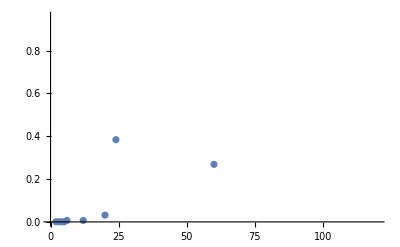

```mathematica
ListPlot[%]
```

## Bethe Vector

### Amplitude Function

```mathematica
Clear[d]
```

```mathematica
A[n_, d_, x_, s_]:= Signature[s]Product[(1 + x[s[[i]]]x[s[[j]]] - 2 d x[s[[i]]])/(1 + x[i] x[j]- 2 d x[i]), {i,1, n-1 }, {j, i+1, n}];
```

```mathematica
B[n_, d_, x_, s_]:= Signature[s]Product[1 + x[s[[i]]]x[s[[j]]] - 2 d x[s[[i]]], {i,1, n-1 }, {j, i+1, n}]Product[x[s[[k]]]^(k-1),{k, 1, n}];
```

```mathematica
A[2,d,  x, {2,1}]
B[2,d,  x, {2,1}]
```

-(1-2 d x[2]+x[1] x[2])/(1-2 d x[1]+x[1] x[2])

-x[1]^2 x[2] (1-2 d x[2]+x[1] x[2])

```mathematica
n =4;
sp = Permutations[Table[i, {i, 1, n}]][[RandomInteger[{1,n!}]]];
sub = Table[x[i]-> 1/x[i], {i, 1, n}];
A[n, d, x, sp]/.sub;
Simplify[A[n, d, x, sp](%)]
```

1

### Bethe coefficients

```mathematica
u[n_, d_, x_, xc_]:=Module[{per, i, j},
per = Permutations[Table[i, {i, 1, n}]];
Return[Sum[A[n, d, x, per[[j]]]Product[x[per[[j]][[i]]]^xc[i], {i, 1, n}], {j, 1, n!}]];
]
```

```mathematica
Clear[d]
u[2 , d, x, xc]
```

x[1]^xc[1] x[2]^xc[2]-(x[1]^xc[2] x[2]^xc[1] (1-2 d x[2]+x[1] x[2]))/(1-2 d x[1]+x[1] x[2])

### Bethe vector

```mathematica
Bv[n_, l_, d_, x_]:= Module[{conf, i,xc},
conf = Subsets[Table[i, {i, 1, l}], {n}];
Return[Table[u[n,d, x, xc]/.Sub[xc, conf[[i]]], {i, 1, Binomial[l, n]}]];
]
```

```mathematica
(*Transfer Matrix*)
TUM [n_, l_, d_]:= Module[{x, br}, 
br= BR[n,l,d,x];
Return[Chop[Bv[n, l, d,x]/.br]];
]
```

```mathematica
TUM[2, 3, d]//MatrixForm
```

(0.+1.73205 ⅈ | 1.5-0.866025 ⅈ | -1.5-0.866025 ⅈ
0.-1.73205 ⅈ | 1.5+0.866025 ⅈ | -1.5+0.866025 ⅈ
0.+1.73205 ⅈ | 0.+1.73205 ⅈ | 0.+1.73205 ⅈ)

```mathematica
(*Transfer Matrix*)
Bv[2, 3, d, x]/.Broots//Chop//MatrixForm
```

(0.+1.73205 ⅈ | 1.5-0.866025 ⅈ | -1.5-0.866025 ⅈ
0.-1.73205 ⅈ | 1.5+0.866025 ⅈ | -1.5+0.866025 ⅈ
0.+1.73205 ⅈ | 0.+1.73205 ⅈ | 0.+1.73205 ⅈ)

## Misc

```mathematica
n =2;
per= Permutations[Table[i, {i, 1, n}]];
ans5 = Sum[B[n, d, x, per[[i]]] B[n, d, z, per[[j]]]/Product[1 - Product[x[per[[i]][[k]]] z[per[[j]][[k]]], {k, i1, n}], {i1, 1, n}], {i, 1, n!}, {j, 1, n!}];
ans5 = Together[ans5];
```

```mathematica
Denominator[ans5]
```

(-1+x[1] z[1]) (-1+x[2] z[1]) (-1+x[1] z[2]) (-1+x[2] z[2])

```mathematica
Clear[d]
```

```mathematica
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 2}]
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 1}]
SeriesCoefficient[Numerator[ans5]/((x[2]-x[1])(z[2]-z[1])), {d, 0, 0}]
```

4 x[1] x[2] z[1] z[2]

-2 (x[1] x[2] z[1]+x[1] x[2] z[2]+x[1] z[1] z[2]+x[2] z[1] z[2])

1+x[1] x[2]+z[1] z[2]+x[1] x[2] z[1] z[2]

```mathematica
Van[n_, x_]:= Product[x[j]-x[i], {i, 1, n-1}, {j, i+1, n}];
```

```mathematica
n =2;
per= Permutations[Table[i, {i, 1, n}]];
ans6 = Sum[B[n, d, x, per[[i]]] B[n, d, z, per[[j]]], {i, 1, n!}, {j, 1, n!}];
ans6 = Together[ans6];
Factor[ans6/(Van[n, x]Van[n,z])]
```

(1+x[1] x[2]) (1+z[1] z[2])

```mathematica
n =6;
per= Permutations[Table[i, {i, 1, n}]];
ans7= Sum[B[n, d, x, per[[i]]] , {i, 1, n!}];
ans7 = Together[ans7];
Factor[ans7/Van[n,x]];
Length[%]
n!Binomial[n,2]
```

13510

10800

```mathematica
N[859/1200]
```

0.715833

```mathematica
Length[%]
```

72

```mathematica
n!Binomial[n,2]
```

144